# Hidden Markov Processes and Viterbi Decoding

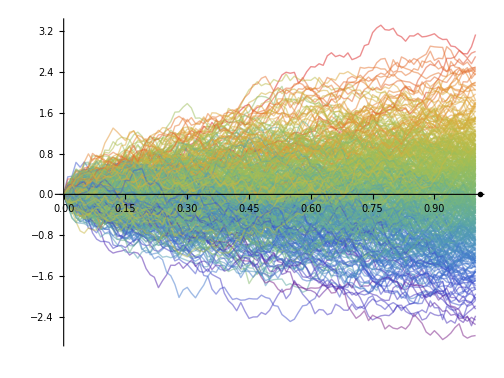

## Bhuvanesh Bhatt, Wolfram Research 10/14/2019

## Markov Processes

A Markov model tells us something about the probabilities of sequences of random variables (states), each of which can take on values from some set. These sets can be words, or tags, or symbols representing anything, such as the weather.

Markov property: the conditional probability distribution of future states of the process (conditional on both past and present states) depends only upon the present state, not on the sequence of events that preceded it (memoryless).

```mathematica
Expectation[x[n+1]\[Conditioned]{x[n],x[n-1],...}]==Expectation[x[n+1]\[Conditioned]x[n]]
```

Markov models are a type of Probabilistic Graphical Model (PGM): a graph expresses the conditional dependence structure between random variables.

DiscreteMarkovProcess

Discrete-time

Finite-state

[wiki]

ContinuousMarkovProcess

Continuous-time

Discrete-state

Adds a Poisson process to the timing of events, but many things remain the same

[wiki]

HiddenMarkovProcess

Discrete-time

Finite-state

The events we are interested in (a sequence of states) are hidden: we don’t observe them directly. For example, we don’t normally observe part-of-speech tags in a text. Rather, we see words, and must infer the tags from the word sequence.

For each state you have distributions specifying the probability of “emissions” (the observable quantities)

Univariate.08 or multivariate emissions

Some states may be “silent”, i.e. they produce no emissions

[wiki]

-Graphics-

## Create Hidden Markov Processes in Mathematica

Define the initial probabilities and the conditional transition probabilities for the hidden states’ dynamics:

```mathematica
p0={1/2,1/2};
tm={{3/4,1/4},{2/5,3/5}};
```

Define hidden Markov process with categorical emissions:

```mathematica
hmm1=HiddenMarkovProcess[p0,tm,{{2/3,1/3},{0,1}}];
```

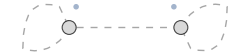

```mathematica
CellPrint[ExpressionCell[viz[BernoulliDistribution[1/3], BernoulliDistribution[1 - 0.01]],"Output",Background->None,ShowCellLabel->False,CellFrame->False]]
```

Define hidden Markov process with general discrete emissions:

```mathematica
hmm2=HiddenMarkovProcess[p0,tm,{GeometricDistribution[1/3],NegativeBinomialDistribution[5,1/4]}];
```

```mathematica
CellPrint[ExpressionCell[viz[GeometricDistribution[1/3],NegativeBinomialDistribution[5,1/4]],"Output",Background->None,ShowCellLabel->False,CellFrame->False]]
```

-Graphics-

Define hidden Markov process with continuous emissions:

```mathematica
hmm3=HiddenMarkovProcess[p0,tm,{NormalDistribution[2,1],StudentTDistribution[-2,1,7]}];
```

```mathematica
CellPrint[ExpressionCell[viz[NormalDistribution[2,1],StudentTDistribution[-2,1,7]],"Output",Background->None,ShowCellLabel->False,CellFrame->False]]
```

-Graphics-

Define hidden Markov processes with multivariate emissions:

```mathematica
hmm4=HiddenMarkovProcess[p0,tm,{MultivariatePoissonDistribution[2,{5,6}],NegativeMultinomialDistribution[6,{1/3,1/4}]}];
```

```mathematica
CellPrint[ExpressionCell[viz3D[MultivariatePoissonDistribution[2,{5,6}],NegativeMultinomialDistribution[6,{1/3,1/4}]],"Output",Background->None,ShowCellLabel->False,CellFrame->False]]
```

-Graphics-

```mathematica
hmm5=HiddenMarkovProcess[p0,tm,
{BinormalDistribution[{-1,2},{1,1},1/2],BinormalDistribution[{2,-1},{1,1},-1/2]}];
```

```mathematica
CellPrint[ExpressionCell[viz3D[BinormalDistribution[{-1,2},{1,1},1/2],BinormalDistribution[{2,-1},{1,1},-1/2]],"Output",Background->None,ShowCellLabel->False,CellFrame->False]]
```

-Graphics-

## Operations on HiddenMarkovProcess

### Simulation (RandomFunction)

Discrete emissions specified by an emission matrix:

TemporalData[…]

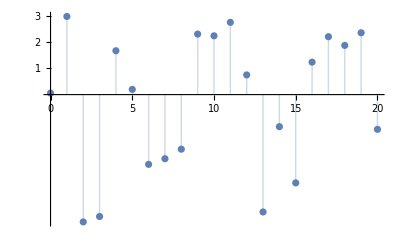

```mathematica
𝒫=HiddenMarkovProcess[{0.5,0.5},{{0.7,0.3},{0.25,0.75}},{NormalDistribution[2,1],StudentTDistribution[-2,1,7]}];
SeedRandom[12345];
data=RandomFunction[𝒫,{0,20}]
ListPlot[data,Filling->Axis,Ticks->{Automatic,{1,2,3}}]
```

```mathematica
data=#->Ceiling[#]&/@Normal[data];
```

```mathematica
sv𝒫=HiddenMarkovProcess[{1/4,3/4},{{0.2,0.8},{0.7,0.3}},{ExponentialDistribution[2],ExponentialDistribution[3]}];
```

Multivariate emissions specified by distributions:

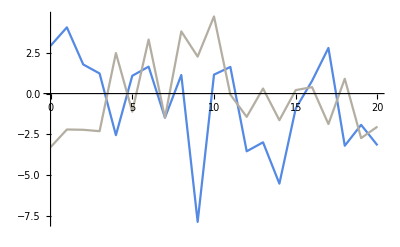

```mathematica
hmm=HiddenMarkovProcess[{0.3,0.7},{{0.5,0.5},{0.3,0.7}},{BinormalDistribution[{-1,1},{2,3},1/2],BinormalDistribution[{1,-1},{3,2},-1/2]}];
SeedRandom[123];
data=RandomFunction[hmm,{0,20}];
ListLinePlot[data]
```

### Process Properties

#### MarkovProcessPropertiespaclet:ref/MarkovProcessProperties — structural, transient, and limiting properties

A hidden Markov process with silent states and discrete emissions:

-Graphics-

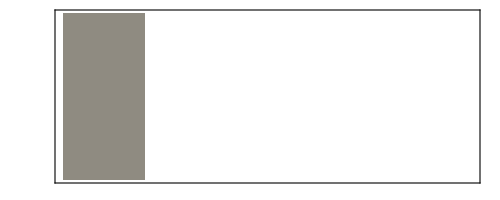
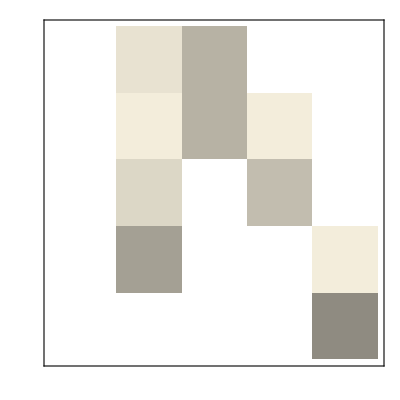
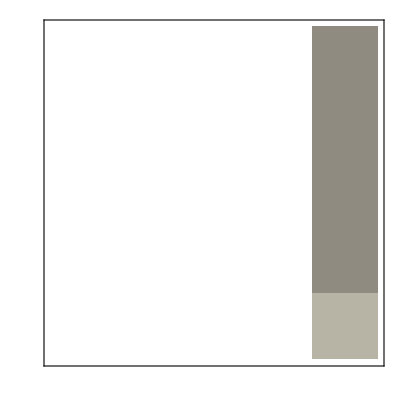
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0,0.111111,0,0,∞}
HoldingTimeVariance | {0,0.123457,0,0,∞}
Structural Properties | 
CommunicatingClasses | {5}, {2,3,4}, {1}
RecurrentClasses | {5}
TransientClasses | {2,3,4}, {1}
AbsorbingClasses | {5}
PeriodicClasses | None
Periods | {∞}
Irreducible | False
Primitive | False
Aperiodic | True
Transient Properties | 
TransientVisitMean | {14.303,12.2424,10.,1.}
TransientVisitVariance | {717.041,773.802,825.921,933.921}
TransientTotalVisitMean | 3.94153
Limiting Properties | 
ReachabilityProbability | {0.,0.944,0.997531,1.,1.}
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
hmm=HiddenMarkovProcess[1,{{0,0.2,0.8,0,0},{0,0.1,0.8,0.1,0},{0,0.3,0,0.7,0},{0,0.9,0,0,0.1},{0,0,0,0,1}},{None,{0.4,0.6,0},{0,0,0},None,{0,0,1}}];
dmm=DiscreteMarkovProcess@hmm;
Graph[dmm]
MarkovProcessProperties[dmm]
```

#### Effective hidden Markov process with silent states eliminated

```mathematica
hmm=HiddenMarkovProcess[1,{{0,0.2,0.8,0,0},{0,0.1,0.8,0.1,0},{0,0.3,0,0.7,0},{0,0.9,0,0,0.1},{0,0,0,0,1}},{None,{0.4,0.6,0},{0,0,0},None,{0,0,1}}];
HiddenMarkovProcess[hmm]
```

HiddenMarkovProcess[{0.944,0.056},{{0.934,0.066},{0.,1.}},{{0.4,0.6,0},{0,0,1}}]

#### LogLikelihoodpaclet:ref/LogLikelihood of a sequence of emissions

```mathematica
hmm=HiddenMarkovProcess[{0.3,0.7},{{0.5,0.5},{0.3,0.7}},{NormalDistribution[-1,1],NormalDistribution[1,1]}];
LogLikelihood[hmm,{{-0.1,0.3,0.9,0.1}}]
```

-5.45624

#### Time slice distribution

```mathematica
hmm=HiddenMarkovProcess[{1/3,2/3},{{1/4,3/4},{3/5,2/5}},{NormalDistribution[m1,s1],NormalDistribution[m2,s2]}];
hmm[t]//Simplify
```

MixtureDistribution[{1/9 (4-(-7/20)^t),1/9 (5+(-7/20)^t)},{NormalDistribution[m1,s1],NormalDistribution[m2,s2]}]

#### PDFpaclet:ref/PDF of the joint distribution of emissions

```mathematica
hmm=HiddenMarkovProcess[{1/3,2/3},{{1/4,3/4},{3/5,2/5}},{{1/2,1/2},{3/7,4/7}}];
PDF[hmm[{2,6}],{e2,e6}]//Expand
```

(7957538767 Boole[1==e2] Boole[1==e6])/37632000000+(9364578871 Boole[1==e6] Boole[2==e2])/37632000000+(9328541233 Boole[1==e2] Boole[2==e6])/37632000000+(3660447043 Boole[2==e2] Boole[2==e6])/12544000000

#### Stationary distribution

```mathematica
hmm=HiddenMarkovProcess[{0.5,0.5},{{0.7,0.3},{0.25,0.75}},{{0.2,0.6,0.2},{0.4,0.2,0.4}}];
```

```mathematica
Probability[e[Infinity]==k,e\[Distributed]hmm]
```

0.309091 Boole[1==k]+0.381818 Boole[2==k]+0.309091 Boole[3==k]

```mathematica
StationaryDistribution[HiddenMarkovProcess[{0.3,0.7},{{0.95,0.05},{0.1,0.9}},{ExponentialDistribution[2],ErlangDistribution[2,3]}]]
```

MixtureDistribution[{0.666667,0.333333},{ExponentialDistribution[2],ErlangDistribution[2,3]}]

#### Process Moments

##### Meanpaclet:ref/Mean — mean function for a process

```mathematica
Mean[HiddenMarkovProcess[{1/3,2/3},{{8/10,2/10},{1/10,9/10}},{ExponentialDistribution[2],ErlangDistribution[2,3]}][t]]//Simplify
```

11/18

```mathematica
Covariance[HiddenMarkovProcess[{2/5,3/5},{{1/2,1/2},{2/5,3/5}},{BinormalDistribution[1/3],BinormalDistribution[2/3]}][t]]//FullSimplify
```

{{1,2/135 (35+10^-t)},{2/135 (35+10^-t),1}}

##### CovarianceFunctionpaclet:ref/CovarianceFunction — covariance function for a process

```mathematica
CovarianceFunction[HiddenMarkovProcess[{3/10,7/10},{{8/10,2/10},{1/10,9/10}},{NormalDistribution[-1/10,2/5],NormalDistribution[4/3,1/4]}],s,t]//Simplify
```

Piecewise[{{-1849/81 7^(-s+t) 10^(-4-s-t) (7^s 10^(1+s)-2^(3+2 s) 25^(1+s)+49^s), s<t}, {-1849/81 7^(s-t) 10^(-4-s-t) (7^t 10^(1+t)-2^(3+2 t) 25^(1+t)+49^t), s>t}, {(893500-1849 (7/5)^(2 s) 2^(1-2 s)-1207 2^-s 5^(1-s) 7^(1+s))/1620000, True}}]

##### CorrelationFunctionpaclet:ref/CorrelationFunction, AbsoluteCorrelationFunctionpaclet:ref/AbsoluteCorrelationFunction — correlation function at lags or times

```mathematica
proc=HiddenMarkovProcess[{0.3,0.7},{{0.95,0.05},{0.1,0.9}},{NormalDistribution[-0.1,0.03],NormalDistribution[0.4,0.05]}];DiscretePlot3D[CorrelationFunction[proc,s,t]//Evaluate,{s,0,10},{t,0,10},ExtentSize->1/2,ColorFunction->"Rainbow"]
```

-Graphics3D-

### Probabilities (Probability, NProbability) and expectations (Expectation, NExpectation)

Imagine a factory process where the hidden states are “good” and “poor” and the emissions “accept” and “unaccept” refer to the condition of the final product.

```mathematica
{good,poor}={1,2};
tm=SparseArray[{{{good,good},{good,poor}}->{0.9,0.1},{poor,poor}->1}];
```

```mathematica
{accept,unaccept}={1,2};
em=SparseArray[{{{good,accept},{good,unaccept}}->{0.99,0.01},{{poor,accept},{poor,unaccept}}->{0.96,0.04}}];
```

```mathematica
p0=SparseArray[{good->0.8,poor->0.2}];
hmm=HiddenMarkovProcess[p0,tm,em];
```

```mathematica
Probability[x[2]==1&&x[1]==1\[Conditioned]x[0]==1,x\[Distributed]hmm]
```

0.961825

```mathematica
Expectation[x[2]+x[5]^2,x\[Distributed]hmm]
```

2.09804

### Parameter estimation (EstimatedProcess, FindProcessParameters)

#### Supervised (with state and emissions data)

#### Unsupervised (only emission data)

Baum-Welch forward-backward version of EM algorithm

Iteratively re-estimates the parameters of the hidden Markov model to improve the probability of observing the given data

Local optimizer, so sensitive to starting points

Estimate a two-state model with exponential emissions:

```mathematica
data=TemporalData[…];
```

```mathematica
class=HiddenMarkovProcess[2,ExponentialDistribution[λ]];
```

Provide a starting value for the process estimate:

```mathematica
sv𝒫=HiddenMarkovProcess[{1/4,3/4},{{0.2,0.8},{0.7,0.3}},{ExponentialDistribution[2],ExponentialDistribution[3]}];
```

Estimate the process using sv𝒫 as an initial model:

```mathematica
EstimatedProcess[data,class,sv𝒫]
```

HiddenMarkovProcess[{0.256679,0.743321},(0.372256 | 0.627744
0.820937 | 0.179063),{ExponentialDistribution[1.63797],ExponentialDistribution[3.22361]}]

```mathematica
EstimatedProcess[data,class,sv𝒫,ProcessEstimator->"ViterbiTraining"]
```

HiddenMarkovProcess[{0.,1.},(0. | 1.
1. | 0.),{ExponentialDistribution[2.08065],ExponentialDistribution[2.15426]}]

## Operations on HiddenMarkovProcess (continued)

### Estimating the hidden states from the emissions (FindHiddenMarkovStates)

Possible criteria (more exist, including a combination of Viterbi and Posterior):

“PosteriorDecoding”: maximize likelihood for hidden state at each time

“ViterbiDecoding”: maximize likelihood for hidden state sequence (default)

Special version for silent state case

Uses Viterbi algorithm for finding the state sequence that maximizes the joint probability of the state path and the observation sequence. This is a dynamic programming procedure (i.e. an algorithm that uses a table to store intermediate values) made possible by the fact that the most probable state sequence has maximum probability subsequences.

I will focus on Viterbi with categorical emissions specified by an emission matrix and no silent states

### Viterbi algorithm

Imagine trying to determine past temperatures for a sequence of days based on records of someone eating n ice creams on a given day. For simplicity, let’s label the hidden states “H” (hot day) or “C” (cold day).

For each possible hidden state sequence (e.g. HHH, HHC, HCH, etc.), we could run the forward algorithm and compute the likelihood of the observation sequence given that hidden state sequence, then choose the hidden state sequence with the maximum observation likelihood. But there are an exponentially large number of state sequences, so this would be prohibitively expensive.

Given probability of being in the state for each state at time t-1, for time t we compute the Viterbi probability by taking the most probable of the extensions of the paths that lead to the current cell.

v_t(j)==max_{s_1... s_(t-1)} (P(s_1... s_(t-1),o_1... o_t,s_t==j))==max_(1≤i≤N-1) (v_(t-1)(i) a_ij b_j(o_t)), where
-Graphics-

Forward pass to update the partial likelihoods (the score of the best path ending in state i at time t), with the best state predecessors stored in a matrix of back-pointers.

Then backtrack, starting from the state with the highest score at time T.

Pseudocode:

## Examples

### Hidden Markov process with categorical emissions

Find the most likely hidden state sequence (Viterbi decode) from the given emissions:

```mathematica
𝒫=HiddenMarkovProcess[{0.5,0.5},{{0.7,0.3},{0.25,0.75}},{{0.2,0.6,0.2},{0.4,0.2,0.4}}];
```

```mathematica
FindHiddenMarkovStates[{1,1,1,1,1,2,3,3,1,2,2},𝒫]
```

{2,2,2,2,2,2,2,2,2,1,1}

```mathematica
FindHiddenMarkovStates[{1,1,1,1,1,2,3,3,1,2,2},𝒫,"PosteriorDecoding"]
```

{2,2,2,2,2,1,2,2,2,1,1}

### HMM with categorical emissions and silent states

```mathematica
Subscript[p,0]={1/2,1/3,0,0,1/12,1/12};
𝒫=SparseArray[{{1,2}->0.85,{1,3}->0.15,{2,3}->0.5,{2,4}->0.5,{3,5}->0.65,{3,4}->0.22,{3,6}->0.13,{4,1}->0.25,{4,3}->0.08,{4,5}->0.67,{5,2}->0.3,{5,6}->0.7,{6,4}->0.6,{6,5}->0.4}];
gr=Graph[DiscreteMarkovProcess[Subscript[p,0],𝒫],ImageSize->300,GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{1,1,2,1,1}}]
em={{1/2,1/4,1/8,1/16,1/32,1/32},{1/32,1/2,1/4,1/8,1/16,1/32},None,None,{1/8,1/16,1/32,1/32,1/2,1/4},{1/4,1/8,1/16,1/32,1/32,1/2}};
```

```mathematica
hmm=HiddenMarkovProcess[Subscript[p,0],𝒫,em];
emissions=RandomFunction[hmm,{0,15}];
likelyPath=FindHiddenMarkovStates[emissions,hmm];
verticesVisited=likelyPath["Values"];
edgesTraversed=DirectedEdge@@@Partition[verticesVisited,2,1];
```

-Graphics-

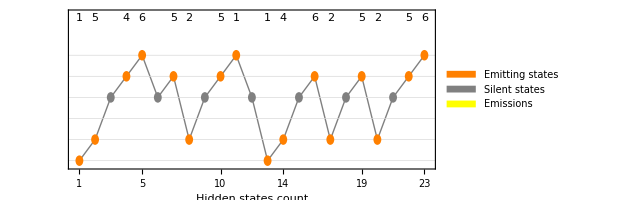

```mathematica
emissionTimes=Pick[likelyPath["Times"],verticesVisited,Except[3|4,_Integer]];
CellPrint[ExpressionCell[Legended[Graphics[{
{{Black,Inset[Framed[Style[Last[#],Small],RoundingRadius->0,Background->Yellow],Most[#],Top]}&/@Transpose[{emissionTimes,ConstantArray[8,Length[emissionTimes]],emissions["Values"]}]},
{Gray,Block[{x=0},Line[{x++,#}&/@verticesVisited]]},Block[{x=0},{If[MemberQ[{3,4},#],Gray,Orange],Disk[{x++,#},0.25]}&/@verticesVisited]},GridLines->{None,Range[6]},GridLinesStyle->LightGray,ImageSize->460,Frame->{{None,True},{True,True}},FrameTicks->{{None,Range[6]},{Transpose[{emissionTimes,1+emissionTimes}],Transpose[{emissionTimes,Range[Length[emissionTimes]]}]}},FrameLabel->{{None,None},{"Hidden states count","Emissions count"}}],
SwatchLegend[{Orange,Gray,Yellow},{"Emitting states","Silent states","Emissions"}]],"Output",Background->None,ShowCellLabel->False,CellFrame->False]]
```

### HMM with continuous emissions

```mathematica
𝒫=HiddenMarkovProcess[{0.3,0.7},{{0.95,0.05},{0.1,0.9}},{ExponentialDistribution[2],ErlangDistribution[2,3]}];
SeedRandom[42];
data=RandomFunction[𝒫,{0,50}]
FindHiddenMarkovStates[data,𝒫]
```

TemporalData[…]

TemporalData[…]

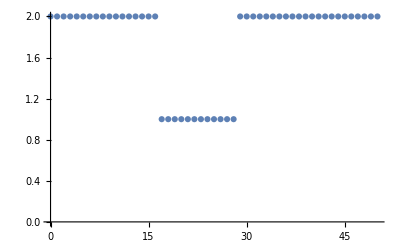

```mathematica
ListPlot[%]
```

## HMM Applications

### Speech Processing

Recognition

Translation

Synthesis

Tagging (parts of speech, or vowels vs consonants)

Classify the characters from sample text into vowels and consonants using a two-state HMM:

```mathematica
text=ExampleData[{"Text","DeclarationOfIndependence"}];
```

```mathematica
chars=Append[CharacterRange["a","z"]," "];
```

```mathematica
data=Cases[ToLowerCase[Flatten[Characters[text]]],Alternatives@@chars]/.Thread[chars->Range[27]];
```

Find the best parameter estimate:

```mathematica
proc=EstimatedProcess[data,HiddenMarkovProcess[2,27],PrecisionGoal->MachinePrecision,AccuracyGoal->MachinePrecision];
```

For each character, pick the state with highest probability from the emission matrix:

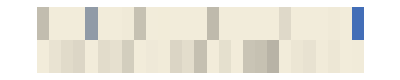

```mathematica
ArrayPlot[em=Last[proc]]
```

```mathematica
res={chars,Cases[Transpose[em],{pv_,pc_}:>If[pv≥pc,"vowel","consonant"]]}//Transpose;
```

```mathematica
GroupBy[res,Extract[2]->Extract[1]]
```

<|vowel→{a,e,i,o,u, },consonant→{b,c,d,f,g,h,j,k,l,m,n,p,q,r,s,t,v,w,x,y,z}|>

### Gene Processing

Recognition

Prediction

Folding

Alignment

### Interface Processing

Gesture Recognition

[Wikipedia]

## Markov Model Resources

### Books

#### Markov Chains

[1983] John G. Kemeny and J. Laurie Snell, Finite Markov Chains, Springer, 1983 [amazon]

[1993] S.P. Meyn and R.L. Tweedie, Markov Chains and Stochastic Stability, Springer, 1993 [amazon] [book] [pdfs]

[1994] William J. Stewart, Introduction to the Numerical Solution of Markov Chains, Princeton University Press, 1994 [amazon]

[1996] Hwei Hsu, Probability, Random Variables & Random Processes, McGraw-Hill, 1996 [amazon] (Section 5.5)

[1998] J.R. Norris, Markov Chains, Cambridge University Press, 1998 [amazon]

[1999] Saber N. Elaydi, An Introduction to Difference Equations,  Second Edition, Springer-Verlag, New York, 1999 (Section 3.5.1)

[2002] Olle Häggström, Finite Markov Chains and Algorithmic Applications, Cambridge University Press, 2002 [amazon]

[2006] Sheldon Ross, Introduction to Probability Models, 9th Edition, Academic Press, 2006 [amazon] (Chapter 4)

[2009] S.P. Meyn and R.L. Tweedie, Markov Chains and Stochastic Stability, Second Edition, Springer, 2009  [amazon]

[2008] Dimitri P. Bertsekas and John N. Tsitsiklis, Introduction to Probability, 2nd Edition, Athena Scientific, 2008 [amazon] (Chapter 7)

[2008] Pierre Bremaud, Markov Chains, Springer, 2008 [amazon]

#### Special Topic: Markov Chain Monte Carlo

[1995] W.R. Gilks, S. Richardson and David Spiegelhalter (eds), Markov Chain Monte Carlo in Practice: Interdisciplinary Statistics, Chapman & Hall, 1995 [amazon]

[2003] George Fishman, Monte Carlo, Springer, 2003 [amazon]

[2005] Christian P. Robert and George Casella, Monte Carlo Statistical Methods, Second Edition, Springer, 2005 [amazon]

[2006] Dani Gamerman and Hedibert F. Lopes, Markov Chain Monte Carlo: Stochastic Simulation for Bayesian Inference, Second Edition, Chapman & Hall, 2006 [amazon]

#### Special Topic: Nonnegative Matrices

[1987] A. Graham, Nonnegative Matrices and Applicable Topics in Linear Algebra, John Wiley&Sons, New York, 1987

[1988] Henryk Minc, Nonnegative matrices, John Wiley&Sons, New York, 1988

[2000] Carl D. Meyer, Matrix Analysis and Applied Linear Algebra, SIAM, 2000 (Chapter 8, in particular Section 8.4)

#### Special Topic: Graph Theory

[2006] Jonathan L. Gross and Jay Yellen, Graph Theory and Its Applications, Second Edition, CRC Press, 1998  [amazon]

### Articles

[2008] Persi Diaconis, The Markov Chain Monte Carlo Revolution, Bulletin of AMS, Volume 46, Number 2, 2009, pp. 179-205 [pdf]

### Webs

Markov Chain [wiki] [mathworld]
Examples of Markov Chains [wiki]
Hidden Markov Model [wiki]
Markov Chain Monte Carlo [wiki]

Mark V Shaney [wiki]

### Software

#### Mathematica, Statistical Inference Package

Check on MixedModel for mixed effects model ... (just noticed this one).

MarkovChainModel: [Time-homogeneous, means that the transition probabilities are independent of the index at which they are given.]

MarkovChainModel[s, n] represents the statistical model for n observations from a time-homogeneous Markov chain with s as number of states or a list of possible states.

Example: MarkovChainModel[3,10] represents the statistical model for 10 observations from time-homogeneous Markov chain with 1, 2, and 3 as possible states.

Example: MarkovChainModel[{“A”, “C”, “G”, “T”}, 100] represents the statistical model for 100 observations from time-homogeneous Markov chain with “A”, “C”, “G”, and “T” as possible states.

Structure of the parameter is a list of 2 elements, the first of which is the vector of unknown initial probabilities and the second the matrix of unknown transition probabilities.

Option ProcessOrder indicates the order of the Markov chain, that is, on how many previous states the conditional distribution of an observation depends. If the order of the chain is greater than 1 the two elements of the parameter are arrays with appropriate dimensions. The default value is 1.

Option Stationary indicates whether the Markov chain is stationary or not. If the chain is stationary, the initial distribution is a function of the transition probabilities and the parameter of the model consists only from the unknown matrix/array of transition probabilities. The default value is False.

HiddenMarkovModel:

HiddenMarkovModel[m, k, n] represents the statistical model for n observations from a hidden Markov model with k states and m as the emission model for each state such that the emission models of states have their own parameters.

HiddenMarkovModel[{("m")_1, ("m")_2, … ("m")_k}, n] represents the statistical model for n observations from a hidden Markov model with k states and the statistical models in the list {("m")_1, ("m")_2, … ("m")_k} as the emission models for each state such that the emission models of states have their own parameters.

HiddenMarkovModel[{("m")_1, ("m")_2, … ("m")_k}] represents the statistical model for  a hidden Markov model with k states and models in the list {("m")_1, ("m")_2, … ("m")_k} as the emission models for each state such that the emission models of states have their own parameters. In this case the models in the list must have the type IndependenceModelWithCommonParameters.

MarkovProcessModel

#### Matlab, Statistics Toolbox

It kind of sounds like their Markov Chain is identical to their Hidden Markov Model ... also it seems that basically a finite probability distribution is allowed as the emissions model for each state. It seems that SIP has a more flexible structure.

Markov Chains: Notice the emmisions matrix ... and emissions symbols.

Markov chains are mathematical descriptions of Markov models with a discrete set of states. Markov chains are characterized by:
    * A set of states {1, 2, ..., M}
    * An M-by-M transition matrix T whose i, j entry is the probability of a transition from state i to state j. The sum of the entries in each row of T must be 1, because this is the sum of the probabilities of making a transition from a given state to each of the other states.
    * A set of possible outputs, or emissions, {s1, s2, ... , sN}. By default, the set of emissions is {1, 2, ... , N}, where N is the number of possible emissions, but you can choose a different set of numbers or symbols.
    *An M-by-N emission matrix E whose i,k entry gives the probability of emitting symbol sk given that the model is in state i.

Hidden Markov Model:

A hidden Markov model is one in which you observe a sequence of emissions, but do not know the sequence of states the model went through to generate the emissions. Analyses of hidden Markov models seek to recover the sequence of states from the observed data.

## HMM Resources

### Books

[1994] Robert J. Elliot, Hidden Markov Models: Estimation and Control, Springer, 1994 [amazon]

[1997] Iain L. MacDonald and Walter Zucchini, Hidden Markov and Other Models for Discrete- valued Time Series, Chapman & Hall, 1997 [amazon]

[2002] Timo Koski, Hidden Markov Models of Bioinformatics, Springer, 2002 [amazon]

[2008] Mark Gales and Steve Young, The Application of Hidden Markov Models in Speech Recognition, Now Publishers, 2008 [amazon]

[2008] Martin Gollery, Handbook of Hidden Markov Models in Bioinformatics, Chapman & Hall, 2008 [amazon]

[2008] Kwan Yi, Hidden Markov Model for Text Classification using LC Classification: Framework, Design, and Application, VDM Verlag, 2008 [amazon]

[2009] Walter Zucchini and Iain L. MacDonald, Hidden Markov Models for Time Series: An Introduction Using R, Chapman & Hall, 2009 [amazon]

[2009] Andrew M. Fraser, Hidden Markov Models and Dynamical Systems, SIAM, 2009 [amazon]

[2009] Patrick Clemins, Automatic Classification of Animal Vocalizations: Generalized Perceptual Linear Prediction Features with Hidden Markov Models, VDM Verlag, 2009 [amazon]

[2010] Olivier Cappe, Eric Moulines and Tobias Ryden, Inference in Hidden Markov Models, Second Edition, Springer 2010 [amazon]

[2010] Rogemar S. Mamon and Robert J. Elliot (eds), Hidden Markov Models in Finance, Springer, 2010 [amazon]

[2010] Ramaprasad Bhar and Shigeyuki Hamori, Hidden Markov Models: Applications to Financial Economics, Springer, 2010 [amazon]

[2010] Ibrahim Yassin Hamid, Automatic Information Extraction Using Hidden Markov Model: Amharic Language Text, VDM Verlag, 2010 [amazon]

[2010] Cesar Guerrero, Available Bandwidth Estimation: A Hidden Markov Model Approach, LAP LAMBERT, 2010 [amazon]

### Webs and Articles

• Classic HMM tutorials by Lawrence Rabiner [web, web]

• Hidden Markov Model (HMM) [wiki] [Nature]
• Poisson Hidden Markov Model (PHMM) [wiki]
• Hidden Semi-Markov Model (HSMM) [wiki]
• Hierarchical Hidden Markov Model (HHMM) [wiki]
• Layered Hidden Markov Model (LHMM) [wiki]
(not a complete list of types of HMMs)

• Viterbi Algorithm [wiki] (optimal state observer for HMMs)
• Baum-Welch Algorithm [wiki] (parameter identification for HMMs)

### Software

#### Matlab Packages

• HMM Toolbox for Matlab [web]

#### R Packages

• HMM [web] [pdf]

#### Python Package

• GHMM [web]

#### Mathematica

• Built-in [web]

#### C Package

• HTK [web]

#### Haskell Package

• hmm [web]

#### Java Package

• jahmm [web]

#### Gene Sequence Applications

• HMMER [wiki] (HMM based program for identifying similar protein or nucleotide sequences)
• HHpred, HHsearch [wiki] (HMM based program for protein search)

#### Gesture Recognition Applications

• gt2k [web]

## Conclusion

The task is not so much to see what no one has yet seen, but rather to think what no one has yet thought, about that which everyone sees.
		― Erwin Schrödinger, physicist